### Marco Teórico

La altura varía con el tiempo de la siguiente manera. Donde primero defino las constantes globales. Dependiendo del experimento evalúo H y A.

```mathematica
a=0.5^2 (*cm*);
g = 980.665 (*cm/s^2*);
hvst[t_] :=(√H-Cd/(√(1-(a/A)^2))a/A √(g/2)(t))^2
```

Ahora cargo los resultados que guardé para generar las gráficas de cada medición. El coeficiente de descarga (de contracción) determina la corrección del resultado teórico de acuerdo con el resultado experimental. Se ajustan a variaciones de la velocidad de descarga de acuerdo con vena contracta y la forma del agujero. Como es circular el coeficiente c_d debe ser de ~0.65.

```mathematica
coeficienteDescarga[t_,h_]:=1/t √(1-(a/A)^2)A/a √(2/g)(√H-√h);
```

#### Recipiente Pequeño.

### Primera Medición.

```mathematica
Al=Max[Drop[Drop[Import["pequeno1.mx"],9],-36][[All,2]]]
```

12.9

```mathematica
(*Resultados y Regresión*)
pequeno1 = MapAt[Function[x,Al-x],Drop[Drop[Import["pequeno1.mx"],9],-36],{All,2}];
pequeno1 = MapAt[Function[x,x-pequeno1[[1,1]]],pequeno1,{All,1}];
trendLinePequeno1 = Fit[pequeno1,{1,x,x^2},x]
```

5.40497-0.0443086 x-0.000875612 x^2

```mathematica
(*Condiciones*)
A=10.7^2;
Cd=1;
H=pequeno1[[1,2]]
```

5.5

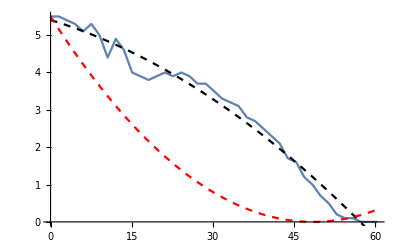

```mathematica
Show[ListLinePlot[pequeno1],Plot[trendLinePequeno1,{x,0,60},PlotStyle->{Black,Dashed}],Plot[hvst[x],{x,0,60},PlotStyle->{Red,Dashed}]]
```

Modifico el resultado deteminando el coeficiente de descarga. Para luego multiplicarlo en la función predicha por Bernoulli. En general el coeficiente de dercarga lo encontré como variable en el tiempo pero tomo simplemente el promedio por practicidad.

```mathematica
trendLinePequeno1Function[x_] := 5.404972402546007-0.044308637577541526 x-0.0008756121691617839 x^2;
Cd = Mean[Table[coeficienteDescarga[pequeno1[[i,1]],trendLinePequeno1Function[pequeno1[[i,1]]]],{i,2,Length[pequeno1]-20}]]
```

1.11198

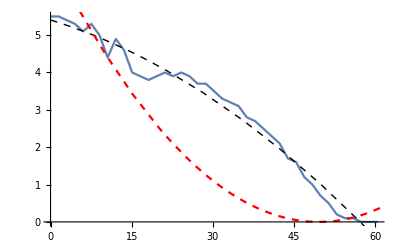

```mathematica
Show[ListLinePlot[pequeno1],Plot[trendLinePequeno1,{x,0,350},PlotStyle->{Black,Dashed,Thick}],Plot[hvst[t],{t,0,250},PlotStyle->{Red,Dashed}]]
```

### Segunda Medición.

```mathematica
Al=Max[Drop[Drop[Import["pequeno2.mx"],10],0][[All,2]]]
```

13.3

```mathematica
(*Resultados y Regresión*)
pequeno2 = MapAt[Function[x,Al-x],Drop[Drop[Import["pequeno2.mx"],10],0],{All,2}];
pequeno2 = MapAt[Function[x,x-pequeno2[[1,1]]],pequeno2,{All,1}];
trendLinePequeno2 = Fit[pequeno2,{1,x,x^2},x]
```

6.95965-0.10583 x-5.99514×10^-6 x^2

```mathematica
(*Condiciones*)
A=10.7^2;
Cd=1;
H=pequeno2[[1,2]]
```

7.1

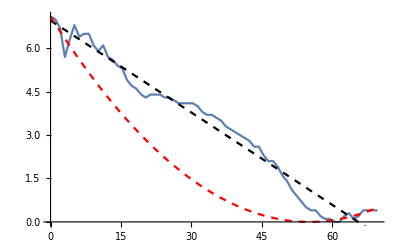

```mathematica
Show[ListLinePlot[pequeno2],Plot[trendLinePequeno2,{x,0,70},PlotStyle->{Black,Dashed}],Plot[hvst[x],{x,0,70},PlotStyle->{Red,Dashed}]]
```

Modifico el resultado deteminando el coeficiente de descarga. Para luego multiplicarlo en la función predicha por Bernoulli. En general el coeficiente de dercarga lo encontré como variable en el tiempo pero tomo simplemente el promedio por practicidad.

```mathematica
trendLinePequeno2Function[x_] := 6.959645205959479-0.10582979815316258 x-5.9951363362429105*10^-6 x^2;
Cd = Mean[Table[coeficienteDescarga[pequeno2[[i,1]],trendLinePequeno2Function[pequeno2[[i,1]]]],{i,2,Length[pequeno2]-10}]]
```

0.535907

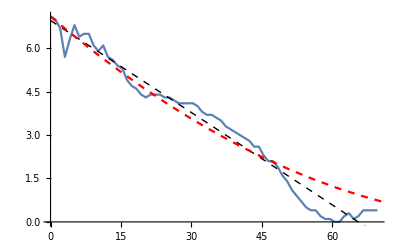

```mathematica
Show[ListLinePlot[pequeno2],Plot[trendLinePequeno2,{x,0,350},PlotStyle->{Black,Dashed,Thick}],Plot[hvst[t],{t,0,250},PlotStyle->{Red,Dashed}]]
```

### Tercera Medición.

```mathematica
Al=Max[Drop[Drop[Import["pequeno3.mx"],14],0][[All,2]]]
```

13.5

```mathematica
(*Resultados y Regresión*)
pequeno3 = MapAt[Function[x,Al-x],Drop[Drop[Import["pequeno3.mx"],14],0],{All,2}];
pequeno3 = MapAt[Function[x,x-pequeno3[[1,1]]],pequeno3,{All,1}];
trendLinePequeno3 = Fit[pequeno3,{1,x,x^2},x]
```

7.27165-0.0862512 x-0.000394502 x^2

```mathematica
(*Condiciones*)
A=10.7^2;
Cd=1;
H=pequeno3[[1,2]]
```

7.4

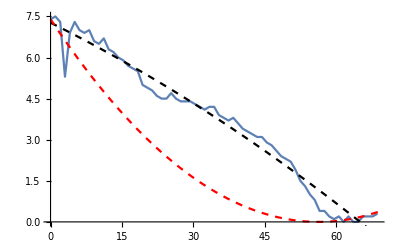

```mathematica
Show[ListLinePlot[pequeno3],Plot[trendLinePequeno3,{x,0,70},PlotStyle->{Black,Dashed}],Plot[hvst[x],{x,0,70},PlotStyle->{Red,Dashed}]]
```

Modifico el resultado deteminando el coeficiente de descarga. Para luego multiplicarlo en la función predicha por Bernoulli. En general el coeficiente de dercarga lo encontré como variable en el tiempo pero tomo simplemente el promedio por practicidad.

```mathematica
trendLinePequeno3Function[x_] := 7.271651745434984-0.08625121351540892 x-0.00039450237751649167 x^2;
Cd = Mean[Table[coeficienteDescarga[pequeno3[[i,1]],trendLinePequeno3Function[pequeno3[[i,1]]]],{i,2,Length[pequeno3]-10}]]
```

0.478472

Si calculo el coeficiente de descarga experimentalmente encuentro el siguiente resultado.

```mathematica
Cd=0.678995589
```

0.678996

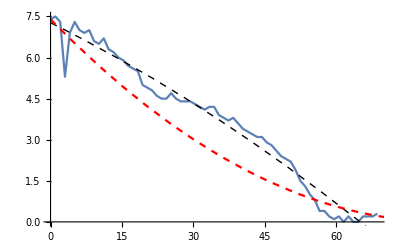

```mathematica
Show[ListLinePlot[pequeno3],Plot[trendLinePequeno3,{x,0,350},PlotStyle->{Black,Dashed,Thick}],Plot[hvst[t],{t,0,250},PlotStyle->{Red,Dashed}]]
```

### Cuarta Medida.

```mathematica
Al=Max[Drop[Drop[Import["pequeno4.mx"],0],0][[All,2]]]
```

12.9

```mathematica
(*Resultados y Regresión*)
pequeno4 = MapAt[Function[x,Al-x],Drop[Drop[Import["pequeno4.mx"],0],0],{All,2}];
pequeno4 = MapAt[Function[x,x-pequeno4[[1,1]]],pequeno4,{All,1}];
trendLinePequeno4 = Fit[pequeno4,{1,x,x^2},x]
```

7.57859-0.133053 x+0.000474975 x^2

```mathematica
(*Condiciones*)
A=10.7^2;
Cd=1;
H=pequeno4[[1,2]]
```

7.4

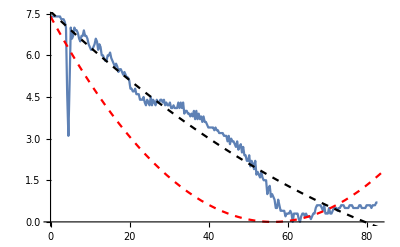

```mathematica
Show[ListLinePlot[pequeno4],Plot[trendLinePequeno4,{x,0,85},PlotStyle->{Black,Dashed}],Plot[hvst[x],{x,0,85},PlotStyle->{Red,Dashed}]]
```

Modifico el resultado deteminando el coeficiente de descarga. Para luego multiplicarlo en la función predicha por Bernoulli. En general el coeficiente de dercarga lo encontré como variable en el tiempo pero tomo simplemente el promedio por practicidad.

```mathematica
trendLinePequeno4Function[x_] := 7.578590372126173-0.13305325328462037 x+0.0004749750030573231 x^2;
Cd = Mean[Table[coeficienteDescarga[pequeno4[[i,1]],trendLinePequeno4Function[pequeno4[[i,1]]]],{i,2,Length[pequeno4]-15}]]
```

0.482493

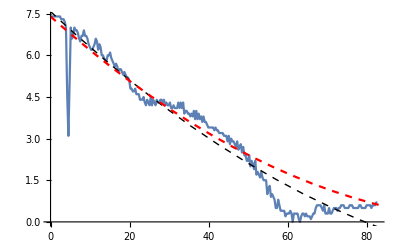

```mathematica
Show[ListLinePlot[pequeno4],Plot[trendLinePequeno4,{x,0,350},PlotStyle->{Black,Dashed,Thick}],Plot[hvst[t],{t,0,250},PlotStyle->{Red,Dashed}]]
```

### Quinta Medida.

```mathematica
Al=Max[Drop[Drop[Import["pequeno5.mx"],28],0][[All,2]]]
```

13.

```mathematica
(*Resultados y Regresión*)
pequeno5 = MapAt[Function[x,Al-x],Drop[Drop[Import["pequeno5.mx"],28],0],{All,2}];
pequeno5 = MapAt[Function[x,x-pequeno5[[1,1]]],pequeno5,{All,1}];
trendLinePequeno5 = Fit[pequeno5,{1,x,x^2},x]
```

7.95027-0.130068 x+0.000351089 x^2

```mathematica
(*Condiciones*)
A=10.7^2;
Cd=1;
H=pequeno5[[1,2]]
```

7.5

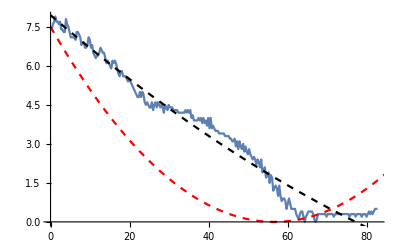

```mathematica
Show[ListLinePlot[pequeno5],Plot[trendLinePequeno5,{x,0,85},PlotStyle->{Black,Dashed}],Plot[hvst[x],{x,0,85},PlotStyle->{Red,Dashed}]]
```

Modifico el resultado deteminando el coeficiente de descarga. Para luego multiplicarlo en la función predicha por Bernoulli. En general el coeficiente de dercarga lo encontré como variable en el tiempo pero tomo simplemente el promedio por practicidad.

```mathematica
trendLinePequeno5Function[x_] := 7.950270668289064-0.13006827892041914 x+0.0003510892115730775 x^2;
Cd = Mean[Table[coeficienteDescarga[pequeno5[[i,1]],trendLinePequeno5Function[pequeno5[[i,1]]]],{i,2,Length[pequeno5]-20}]]
```

0.395506

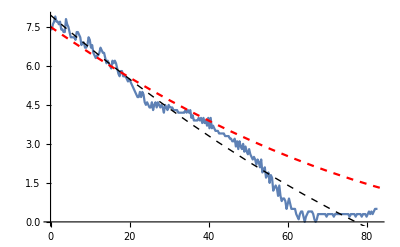

```mathematica
Show[ListLinePlot[pequeno5],Plot[trendLinePequeno5,{x,0,350},PlotStyle->{Black,Dashed,Thick}],Plot[hvst[t],{t,0,250},PlotStyle->{Red,Dashed}]]
```

## Recipiente Mediano.

### Primera Medida.

```mathematica
Al=Max[Drop[Drop[Import["medio1.mx"],1],0][[All,2]]]
```

16.2

```mathematica
(*Resultados y Regresión*)
medio1 = MapAt[Function[x,Al-x],Drop[Drop[Import["medio1.mx"],1],0],{All,2}];
medio1 = MapAt[Function[x,x-medio1[[1,1]]],medio1,{All,1}];
trendLineMedio1 = Fit[medio1,{1,x,x^2},x]
```

10.0808-0.0876341 x+0.000198292 x^2

```mathematica
(*Condiciones*)
A=14^2;
Cd=1;
H=medio1[[1,2]]
```

10.

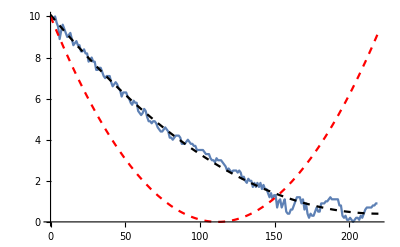

```mathematica
Show[ListLinePlot[medio1],Plot[trendLineMedio1,{x,0,220},PlotStyle->{Black,Dashed}],Plot[hvst[x],{x,0,220},PlotStyle->{Red,Dashed}]]
```

Modifico el resultado deteminando el coeficiente de descarga. Para luego multiplicarlo en la función predicha por Bernoulli. En general el coeficiente de dercarga lo encontré como variable en el tiempo pero tomo simplemente el promedio por practicidad.

```mathematica
trendLineMedio1Function[x_] := 10.08079923667609-0.08763409618464994 x+0.0001982922033841647 x^2;
Cd = Mean[Table[coeficienteDescarga[medio1[[i,1]],trendLineMedio1Function[medio1[[i,1]]]],{i,2,Length[medio1]}]]
```

0.45959

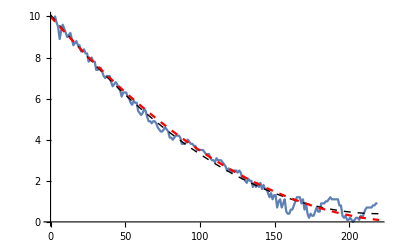

```mathematica
Show[ListLinePlot[medio1],Plot[trendLineMedio1,{x,0,220},PlotStyle->{Black,Dashed,Thick}],Plot[hvst[t],{t,0,220},PlotStyle->{Red,Dashed}]]
```

### Segunda Medida.

```mathematica
Al=Max[Drop[Drop[Import["medio2.mx"],0],0][[All,2]]]
```

16.2

```mathematica
(*Resultados y Regresión*)
medio2 = MapAt[Function[x,Al-x],Drop[Drop[Import["medio2.mx"],0],0],{All,2}];
medio2 = MapAt[Function[x,x-medio2[[1,1]]],medio2,{All,1}];
trendLineMedio2 = Fit[medio2,{1,x,x^2},x]
```

10.4582-0.0855965 x+0.000174645 x^2

```mathematica
(*Condiciones*)
A=14^2;
Cd=1;
H=medio2[[1,2]]
```

10.4

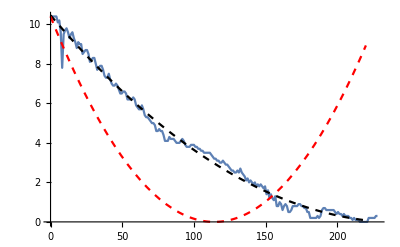

```mathematica
Show[ListLinePlot[medio2],Plot[trendLineMedio2,{x,0,220},PlotStyle->{Black,Dashed}],Plot[hvst[x],{x,0,220},PlotStyle->{Red,Dashed}]]
```

Modifico el resultado deteminando el coeficiente de descarga. Para luego multiplicarlo en la función predicha por Bernoulli. En general el coeficiente de dercarga lo encontré como variable en el tiempo pero tomo simplemente el promedio por practicidad.

```mathematica
trendLineMedio2Function[x_] := 10.458212154323032-0.08559648590850083 x+0.00017464502038287095 x^2;
Cd = Mean[Table[coeficienteDescarga[medio2[[i,1]],trendLineMedio2Function[medio2[[i,1]]]],{i,2,Length[medio2]}]]
```

0.461521

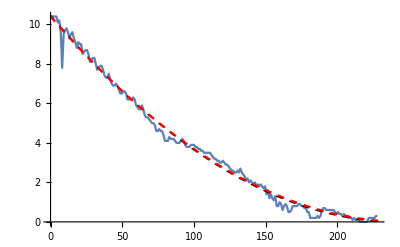

```mathematica
Show[ListLinePlot[medio2],Plot[trendLineMedio2,{x,0,350},PlotStyle->{Black,Dashed,Thick}],Plot[hvst[t],{t,0,250},PlotStyle->{Red,Dashed}]]
```

### Tercera Medida.

```mathematica
Al=Max[Drop[Drop[Import["medio3.mx"],0],0][[All,2]]]
```

16.3

```mathematica
(*Resultados y Regresión*)
medio3 = MapAt[Function[x,Al-x],Drop[Drop[Import["medio3.mx"],0],0],{All,2}];
medio3 = MapAt[Function[x,x-medio3[[1,1]]],medio3,{All,1}];
trendLineMedio3 = Fit[medio3,{1,x,x^2},x]
```

8.54928-0.081035 x+0.000194348 x^2

```mathematica
(*Condiciones*)
A=14^2;
Cd=1;
H=medio3[[1,2]]
```

8.7

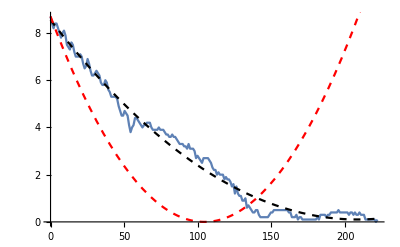

```mathematica
Show[ListLinePlot[medio3],Plot[trendLineMedio3,{x,0,220},PlotStyle->{Black,Dashed}],Plot[hvst[x],{x,0,220},PlotStyle->{Red,Dashed}]]
```

Modifico el resultado deteminando el coeficiente de descarga. Para luego multiplicarlo en la función predicha por Bernoulli. En general el coeficiente de dercarga lo encontré como variable en el tiempo pero tomo simplemente el promedio por practicidad.

```mathematica
trendLineMedio3Function[x_] := 8.549281438233464-0.08103504078437405 x+0.00019434841403030278 x^2;
Cd = Mean[Table[coeficienteDescarga[medio3[[i,1]],trendLineMedio3Function[medio3[[i,1]]]],{i,2,Length[medio3]}]]
```

0.504409

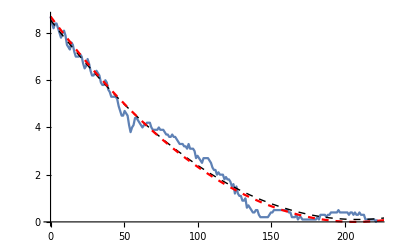

```mathematica
Show[ListLinePlot[medio3],Plot[trendLineMedio3,{x,0,350},PlotStyle->{Black,Dashed,Thick}],Plot[hvst[t],{t,0,250},PlotStyle->{Red,Dashed}]]
```

### Cuarta Medición.

```mathematica
Al=Max[Drop[Drop[Import["medio4.mx"],0],0][[All,2]]]
```

17.4

```mathematica
(*Resultados y Regresión*)
medio4 = MapAt[Function[x,Al-x],Drop[Drop[Import["medio4.mx"],0],0],{All,2}];
medio4 = MapAt[Function[x,x-medio4[[1,1]]],medio4,{All,1}];
trendLineMedio4 = Fit[medio4,{1,x,x^2},x]
```

10.8049-0.0774305 x+0.00010631 x^2

```mathematica
(*Condiciones*)
A=14^2;
Cd=1;
H=medio4[[1,2]]
```

10.5

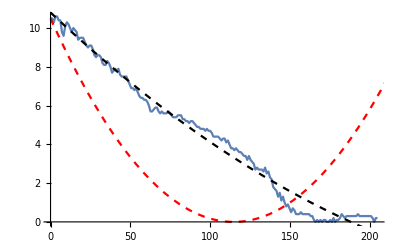

```mathematica
Show[ListLinePlot[medio4],Plot[trendLineMedio4,{x,0,220},PlotStyle->{Black,Dashed}],Plot[hvst[x],{x,0,220},PlotStyle->{Red,Dashed}]]
```

Modifico el resultado deteminando el coeficiente de descarga. Para luego multiplicarlo en la función predicha por Bernoulli. En general el coeficiente de dercarga lo encontré como variable en el tiempo pero tomo simplemente el promedio por practicidad.

```mathematica
trendLineMedio4Function[x_] := 10.804928935003835-0.07743050729873203 x+0.00010631026946781359 x^2;
Cd = Mean[Table[coeficienteDescarga[medio4[[i,1]],trendLineMedio4Function[medio4[[i,1]]]],{i,2,Length[medio4]-20}]]
```

0.400374

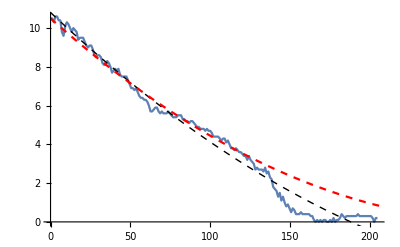

```mathematica
Show[ListLinePlot[medio4],Plot[trendLineMedio4,{x,0,350},PlotStyle->{Black,Dashed,Thick}],Plot[hvst[t],{t,0,250},PlotStyle->{Red,Dashed}]]
```

## Recipiente Grande.

### Primera Medición.

```mathematica
Al=Max[Import["grande1.mx"][[All,2]]]
```

18.1

```mathematica
(*Resultados y Regresión*)
grande1 = MapAt[Function[x,Al-x],Import["grande1.mx"],{All,2}];
grande1 = MapAt[Function[x,x-grande1[[1,1]]],grande1,{All,1}];
trendLineGrande1 = Fit[grande1,{1,x,x^2},x]
```

9.30349-0.0593781 x+0.0000977071 x^2

```mathematica
(*Condiciones*)
A=17^2;
Cd=1;
H=grande1[[1,2]]
```

9.6

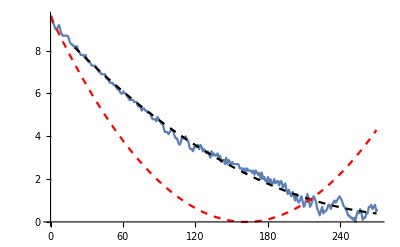

```mathematica
Show[ListLinePlot[grande1],Plot[trendLineGrande1,{x,20,270},PlotStyle->{Black,Dashed}],Plot[hvst[x],{x,0,270},PlotStyle->{Red,Dashed}]]
```

Modifico el resultado deteminando el coeficiente de descarga. Para luego multiplicarlo en la función predicha por Bernoulli. En general el coeficiente de dercarga lo encontré como variable en el tiempo pero tomo simplemente el promedio por practicidad.

```mathematica
trendLineGrande1Function[x_] := 9.303488424763664-0.05937814331928607 x+0.00009770706171665352 x^2;
Cd = Mean[Table[coeficienteDescarga[grande1[[i,1]],trendLineGrande1Function[grande1[[i,1]]]],{i,2,Length[grande1]}]]
```

0.556342

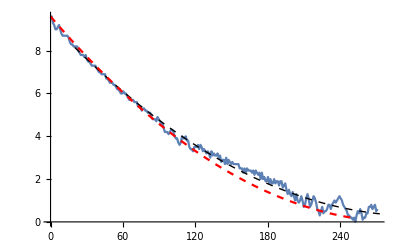

```mathematica
Show[ListLinePlot[grande1],Plot[trendLineGrande1,{x,20,350},PlotStyle->{Black,Dashed,Thick}],Plot[hvst[t],{t,0,250},PlotStyle->{Red,Dashed}]]
```

### Segunda Medición.

```mathematica
Al=Max[Import["grande2.mx"][[All,2]]]
```

18.

```mathematica
(*Resultados y Regresión*)
grande2 = MapAt[Function[x,Al-x],Import["grande2.mx"],{All,2}];
grande2 = MapAt[Function[x,x-grande2[[1,1]]],grande2,{All,1}];
trendLineGrande2 = Fit[grande2,{1,x,x^2},x]
```

9.59333-0.0592993 x+0.0000919115 x^2

```mathematica
(*Condiciones*)
A=17^2;
Cd=1;
H=grande2[[1,2]]
```

9.5

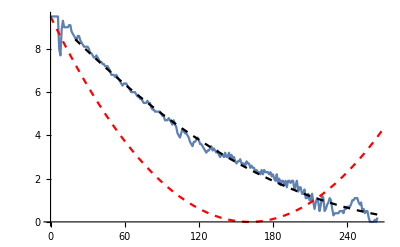

```mathematica
Show[ListLinePlot[grande2],Plot[trendLineGrande2,{x,20,270},PlotStyle->{Black,Dashed}],Plot[hvst[x],{x,0,270},PlotStyle->{Red,Dashed}]]
```

Modifico el resultado deteminando el coeficiente de descarga. Para luego multiplicarlo en la función predicha por Bernoulli.

```mathematica
trendLineGrande2Function[x_] := 9.593325140739823-0.05929928896115123 x+0.00009191149001796324 x^2;
Cd = Mean[Table[coeficienteDescarga[grande2[[i,1]],trendLineGrande2Function[grande2[[i,1]]]],{i,2,Length[grande2]}]]
```

0.480434

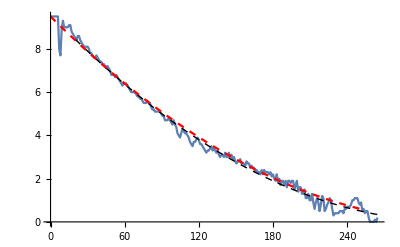

```mathematica
Show[ListLinePlot[grande2],Plot[trendLineGrande2,{x,20,350},PlotStyle->{Black,Dashed,Thick}],Plot[hvst[t],{t,0,250},PlotStyle->{Red,Dashed}]]
```

#### Tercera Medición.

```mathematica
Al=Max[Import["grande3.mx"][[All,2]]]
```

18.1

```mathematica
(*Resultados y Regresión*)
grande3 = MapAt[Function[x,Al-x],Import["grande3.mx"],{All,2}];
grande3 = MapAt[Function[x,x-grande3[[1,1]]],grande3,{All,1}];
trendLineGrande3 = Fit[grande3,{1,x,x^2},x]
```

10.6022-0.0630582 x+0.0000924008 x^2

```mathematica
(*Condiciones*)
A=17^2;
Cd=1;
H=grande3[[1,2]]
```

10.7

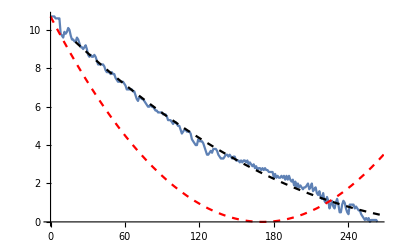

```mathematica
Show[ListLinePlot[grande3],Plot[trendLineGrande3,{x,20,270},PlotStyle->{Black,Dashed}],Plot[hvst[x],{x,0,270},PlotStyle->{Red,Dashed}]]
```

Modifico el resultado deteminando el coeficiente de descarga. Para luego multiplicarlo en la función predicha por Bernoulli.

```mathematica
trendLineGrande3Function[x_] := 10.60223080816294-0.06305818206581668 x+0.00009240082222517816 x^2;
Cd = Mean[Table[coeficienteDescarga[grande3[[i,1]],trendLineGrande3Function[grande3[[i,1]]]],{i,2,Length[grande3]}]]
```

0.527254

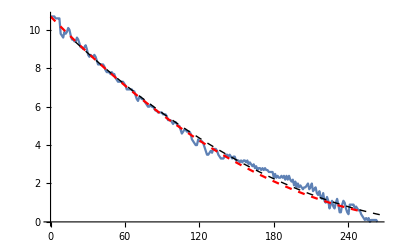

```mathematica
Show[ListLinePlot[grande3],Plot[trendLineGrande3,{x,20,350},PlotStyle->{Black,Dashed,Thick}],Plot[hvst[t],{t,0,250},PlotStyle->{Red,Dashed}]]
```

Cuarta medición.

```mathematica
Al=Max[Import["grande4.mx"][[All,2]]]
```

17.9

```mathematica
(*Resultados y Regresión*)
grande4 = MapAt[Function[x,Al-x],Import["grande4.mx"],{All,2}];
grande4 = MapAt[Function[x,x-grande4[[1,1]]],grande4,{All,1}];
trendLineGrande4 = LinearModelFit[grande4,{1,x,x^2},x]
```

FittedModel[11.4211-0.0690965 x+0.000107683 x^2]

```mathematica
trendLineGrande4[{"RSquared"}]
```

{0.996358}

```mathematica
(*Experimental*)
trendLineGrande4 = Fit[grande4,{1,x,x^2},x]
```

11.4211-0.0690965 x+0.000107683 x^2

```mathematica
(*Condiciones*)
A=17^2;
Cd=1;
H=grande4[[1,2]]
```

11.4

```mathematica
11.399999999999999
```

11.4

```mathematica
(*Teórico*)
hvst[x]
```

(3.37639-0.0191552 x)^2

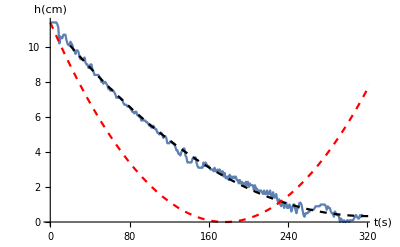

```mathematica
Show[ListLinePlot[grande4],Plot[trendLineGrande4,{x,20,350},PlotStyle->{Black,Dashed}],Plot[hvst[x],{x,0,350},PlotStyle->{Red,Dashed}],AxesLabel-> {"t(s)","h(cm)"}]
```

Modifico el resultado deteminando el coeficiente de descarga. Para luego multiplicarlo en la función predicha por Bernoulli.

```mathematica
trendLineGrande4Function[x_] := 11.421076084294452-0.06909649708752856 x+0.00010768281220172026 x^2;
Cd = Mean[Table[coeficienteDescarga[grande4[[i,1]],trendLineGrande4Function[grande4[[i,1]]]],{i,2,Length[grande4]}]]
```

0.51616

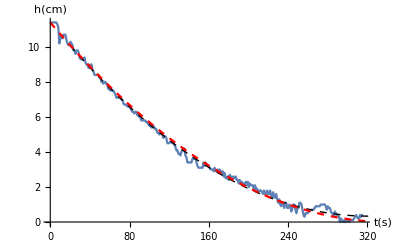

```mathematica
Show[ListLinePlot[grande4],Plot[trendLineGrande4,{x,20,350},PlotStyle->{Black,Dashed,Thick}],Plot[hvst[t],{t,0,350},PlotStyle->{Red,Dashed}], AxesLabel-> {"t(s)","h(cm)"}]
```